## Models of a Box With Friction

### Initial Conditions and Other Global Parameters

```mathematica
F[t_]=5;
Fs=5;
Fk=2;
m=1;
vi=10;
pi=0;
```

### First Model Using Piecewise Functions and Classical Assumptions

#### m y''[t]==F[t]-Piecewise[{{F[t], F[t]≤Fs&&y'[t]==0}, {Fk, y'[t]>0}}];

```mathematica
model1:=Module[{diff,soln},
diff=m y''[t]==F[t]-Piecewise[{{F[t], F[t]≤Fs&&y'[t]==0}, {Fk, y'[t]>0}}];

soln=NDSolve[{diff,y'[0]==vi,y[0]==pi},y,{t,0,25}];

P1=Plot[{y[t]/.soln,y'[t]/.soln,y''[t]/.soln},{t,0,25},
PlotRange->{All,All},
ImageSize->Large,
PlotTheme->{"RoyalColor","ThickLines","Grid"},
PlotLegends->{"Position (m)","Velocity (m/s)","Acceleration (m/s^2)","Applied Force (N)"}];
f1=Plot[{F[t]-(y''[t]/.soln)m,Fk,Fs,F[t]},{t,0,5},
PlotRange->All,
ImageSize->Large];

{P1,f1}
]
```

### Second Piecewise function and Transition Assumptions

#### m y''[t]==F[t]-Piecewise[{{F[t], F[t]≤Fs&&y'[t]==0}, {Fk+(Fs-Fk)ⅇ^(-k y'[t]), F[t]>Fs||y'[t]>0}}];

```mathematica
model2:=Module[{k,diff,soln},
k=1000;

diff=m y''[t]==F[t]-Piecewise[{{F[t], F[t]≤Fs&&y'[t]==0}, {Fk+(Fs-Fk)ⅇ^(-k y'[t]), F[t]>Fs||y'[t]>0}}];

soln=NDSolve[{diff,y'[0]==vi,y[0]==pi},y,{t,0,25}];
P2=Plot[{y[t]/.soln,y'[t]/.soln,y''[t]/.soln},{t,0,25},
PlotRange->All,
ImageSize->Large,
PlotTheme->{"NeonColors","ThickLines","Grid"},
PlotLegends->{"Position (m)","Velocity (m/s)","Acceleration (m/s^2)","Applied Force (N)"}];
f2=Plot[{F[t]-(y''[t]/.soln)m,Fk,Fs,F[t]},{t,0,5},
PlotRange->All,
ImageSize->Large];

{P2,f2}
]
```

### Unified Model: No Piecewise

#### m (ⅆ^2 y⃗(t))/(ⅆ t^2)==F⃗(t)+f⃗; f⃗=-((ⅆ y⃗(t))/ⅆt)/(||(ⅆ y⃗(t))/ⅆt||)(Fk+(fs-Fk)ⅇ^(-k1 ||(ⅆ y⃗(t))/ⅆt||)); fs=Fs+(F⃗(t)-Fs)ⅇ^(-k2 (||F⃗(t)||)/Fs);

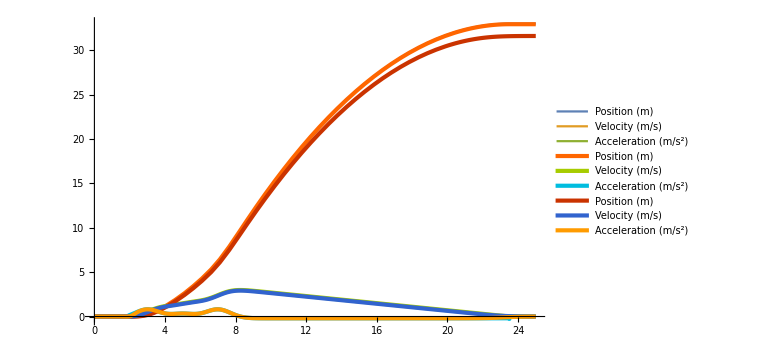

```mathematica
Module[{F,Fs,Fk,fs,f,m,k1,k2,diff,soln},
F[t_]=10 ⅇ^(-((t-3))^2)+5 ⅇ^(-((t-5))^2)+10 ⅇ^(-((t-7))^2);
Fs=3;
Fk=2;
m=10;
k1=10;
k2=.01;

fs=Fs+(F[t]-Fs)ⅇ^(-k2 (F[t])^3);
f=Fk+(fs-Fk)ⅇ^(-k1 y'[t]);

diff={m y''[t]==F[t]-f,
y'[0]==0,
y[0]==0};

soln=NDSolve[diff,y,{t,0,25}];

P3=Plot[{y[t]/.soln,y'[t]/.soln,y''[t]/.soln},{t,0,25},
PlotRange->All,
ImageSize->Large,
PlotTheme->"Web",
PlotLegends->{"Position (m)","Velocity (m/s)","Acceleration (m/s^2)","Applied Force (N)"}];

f3=Plot[{F[t],F[t]-(y''[t]/.soln)m},{t,0,25}];
Show[P1,P2,P3]
]
```

```mathematica
model3:=Module[{f,fs,k1,k2,diff,soln},
k1=1000;
k2=100;

fs=Fs+(F[t]-Fs)ⅇ^(-k2 Abs[F[t]]/Fs);
f=-Sign[y'[t]](Fk+(fs-Fk)ⅇ^(-k1 Abs[y'[t]]));
diff={m y''[t]==F[t]+f,
y'[0]==vi,
y[0]==pi};

soln=NDSolve[diff,y,{t,0,25}];

P3=Plot[{y[t]/.soln,y'[t]/.soln,y''[t]/.soln,F[t]},{t,0,25},
PlotRange->All,
ImageSize->Large,
PlotTheme->{"ThickLines","VibrantColors","Grid"},
PlotLegends->{"Position (m)","Velocity (m/s)","Acceleration (m/s^2)","Applied Force (N)"}];

f3=Plot[{F[t]-(y''[t]/.soln)m,Fk,Fs,F[t],y'[t]/.soln},{t,0,5},
PlotRange->All,
PlotLegends->{"Friction","Kinetic Friction","Static Friction","Applied Force"},
ImageSize->1250];

{P3,f3}
]
```

### Unified Model 2:

### m (ⅆ^2 y⃗(t))/(ⅆ t^2)==F⃗(t)+f⃗ N; f⃗=-((ⅆ y⃗(t))/ⅆt)/(||(ⅆ y⃗(t))/ⅆt||)(kk +(fs-kk )ⅇ^(-k1 ||(ⅆ y⃗(t))/ⅆt||)); fs=ks+((F⃗(t))/N-ks)ⅇ^(-k2 (||F⃗(t)||)/(ks N));

```mathematica
model4[K1_,K2_,KS_,KK_]:=Module[{f,fs,k1,k2,kk,ks,N,diff,soln},
k1=K1;
k2=K2;
N = 9.8 m;
ks=KS;
kk=KK;

fs=ks+(F[t]/N-ks)ⅇ^(-k2 Abs[F[t]]/(ks N));
f=-Sign[y'[t]](kk+(fs-kk)ⅇ^(-k1 Abs[y'[t]]));
diff={m y''[t]==F[t]+f N,
y'[0]==vi,
y[0]==pi};

soln=NDSolve[diff,y,{t,0,10}];

P4=Plot[{y[t]/.soln,y'[t]/.soln,y''[t]/.soln,F[t]},{t,0,10},
PlotRange->All,
ImageSize->Large,
PlotTheme->"Monochrome",
PlotLegends->{"Position (m)","Velocity (m/s)","Acceleration (m/s^2)","Applied Force (N)"}];

f4=Plot[{F[t]-(y''[t]/.soln)m,kk*N,ks*N,F[t],y'[t]/.soln},{t,0,5},
PlotRange->All,
PlotTheme->"Monochrome",
PlotLegends->{"Friction","Kinetic Friction","Static Friction","Applied Force","Velocity"},
ImageSize->1250];

{P4,f4}
]
```

### Combined Models

```mathematica
Manipulate[model4[10,10,1.4,a][[2]],{{a,15},0,30,.1}]
```

```mathematica
}
```